```mathematica
(*rotation matrix*)
rot[th_] :=({{1, 0, 0, 0}, {0, Cos[2 th], Sin[2th], 0}, {0, -Sin[2 th], Cos[2th], 0}, {0, 0, 0, 1}})
(*waveplate matrix*)
wp[th_] :=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[th], Sin[th]}, {0, 0, -Sin[th], Cos[th]}})
(*polariser matrix*)
pol := 1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
matrix =pol.pol
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

matrix = pol.rot.pol
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}.rot.{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*3 pi/4 is the orientation of final polariser, switch to pi/2 for FLC retardance measurement (polariser at 90 deg) *)
matrix =(pol.rot[π/2-theta-a].pol.rot[theta+a].{I0,0,0,0} )[[1]]
Plot[matrix/.{I0->1,a->49.6π/180},{theta,0,2π}]
```

I0 (1/4+1/4 Cos[2 (-a+π/2-theta)])

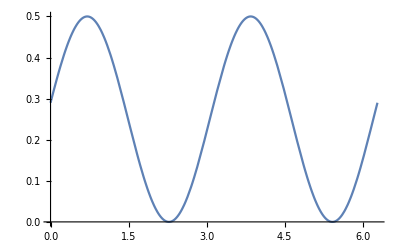

```mathematica
(*3 pi/4 is the orientation of final polariser, switch to pi/2 for FLC retardance measurement (polariser at 90 deg) *)
matrix =(pol.rot[π/2-b].wp[δ].rot[b-theta-a].pol.rot[theta+a].{I0,0,0,0} )[[1]]
Plot[{matrix/.{I0->1,a->49.6π/180,b->0,δ->π-0.1},matrix/.{I0->1,a->49.6π/180,b->0,δ->π+0.1}},{theta,0,2π}]
```

I0 (1/4+1/2 (1/2 Cos[2 (-b+π/2)] Cos[2 (-a+b-theta)]-1/2 Cos[δ] Sin[2 (-b+π/2)] Sin[2 (-a+b-theta)]))

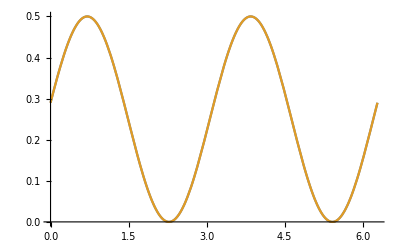

```mathematica
(* - theta is not necessarily the same as +theta, depending on which way the polarisation angle is defined, which will give you a different retardance offset*)
```

I0 (1/4+1/2 (1/2 Cos[2 (-b+π/2)] Cos[2 (-a+b+theta)]-1/2 Cos[δ] Sin[2 (-b+π/2)] Sin[2 (-a+b+theta)]))

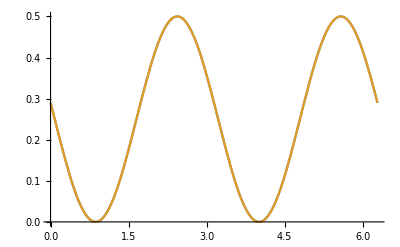

```mathematica
matrix =(pol.rot[π/2-b].wp[δ].rot[b+theta-a].pol.rot[-theta+a].{I0,0,0,0} )[[1]]
Plot[{matrix/.{I0->1,a->49.6π/180,b->0,δ->π-0.1},matrix/.{I0->1,a->49.6π/180,b->0,δ->π+0.1}},{theta,0,2π}]
```